```mathematica
Assignment 6
```

## Karim Sobh 201700836

## Problem 1

```mathematica
tmax = 10; 
dt = 0.001; 
tL = Range[0,tmax,dt]; lt = Length[tL];
 xx0 = 1.0; yy0 =0.0; 
vvx0 = 0.0; vvy0 = 5;
vvxList = Table[0,{i,lt}]; vvyList = vvxList; xxList =vvxList;yyList = vvxList;
vvxList[[1]] = vvx0; vvyList[[1]] = vvy0; 
xxList[[1]]   = xx0;   yyList[[1]]    = yy0; 
e = 0.6; a= 2.5; 
thetaa=Range[1,0.036,360];
thetaaL=Length[thetaa];
Te =vvxList; Ee=vvxList;
Ve = vvxList; vvList=vvxList;
Vedif = vvxList; Tedif=vvxList;
Le=xxList;dAt=xxList; ddAt=xxList;
dthetaa =1;    dLe=xList;
Do[rNormm=(1-e)/(1+e Cos[thetaa[[nt]]]);
vvxList[[nt]] =vvxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNormm;
vvyList[[nt]] =vvyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]];
xxList[[nt]]   = xxList[[nt-1]] + vvxList[[nt]] dt; 
yyList[[nt]]   = yyList[[nt-1]] + vvyList[[nt]] dt;
vvList[[nt]]=Sqrt[vxList[[nt]]^2+vyList[[nt]]^2];
Le[[nt]]=rNormm^2 ; dAt[[nt]]= Le[[nt]]/2; ddAt[[nt]]= dAt[[nt]]- dAt[[nt-1]],{nt,1,lt}];
Table[{Le[[j]],dAt[[nt]],ddAt[[j]]},{j,1,lt}]
```

```mathematica
Problem 2
```

```mathematica
tmax = 10; 
dt = 0.001; 
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = 1.0; y0 =0.0; 
vx0 = 0.0; vy0 = 2.0 Pi;
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
T =vxList;
V = vxList; vList=vxList;
Vdif = vxList; Tdif=vxList;
thetta=xList;L=xList;
dthetta =xList;    dL=xList;
Do[
rNorm                 =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
vList[[nt]]=Sqrt[vxList[[nt]]^2+vyList[[nt]]^2];
thetta[[nt]]=ArcTan[yList[[nt]]/xList[[nt]]];
dthetta[[nt]]=thetta[[nt]]-thetta[[nt-1]];
L[[nt]]=rNorm^2 dthetta[[nt]];
T[[nt]] = vList[[nt]]^2;
V[[nt]]= 4 Pi^2 /rNorm;
Tdif[[nt]]=T[[nt]]-T[[nt-1]]; 
Vdif[[nt]]=V[[nt]]-V[[nt-1]];
dL[[nt]]=L[[nt]]-L[[nt-1]]
,{nt,2,lt}];
Table[{Tdif[[j]],Vdif[[j]],dL[[j]]},{j,lt}]
Table[{T[[i]],V[[i]],L[[i]]},{i,lt}]
(*As seen the differences of Kinetic and Potential gets smaller by time while Angular momentum suffers an abrubt rise till it reaches a too stable point.*)
```

{{0.,0.,1.},{39.48,39.4784,-1.99372},{0.00155855,0.000779265,1.},9995,{0.00155814,0.000778996,1.88333×10^-11},{0.00155833,0.000779109,1.39402×10^-11},{0.00155847,0.000779192,9.04578×10^-12}}
 |  |  |  |

{{0.,0.,1.},{39.48,39.4784,-0.993717},{39.4815,39.4792,0.00628335},{39.4831,39.48,0.00628335},9994,{39.475,39.4759,0.00628335},{39.4766,39.4767,0.00628335},{39.4781,39.4775,0.00628335}}
 |  |  |  |

```mathematica
dt = 0.001; 
tL = Range[0,tmax,dt]; lt = Length[tL];
 xx0 = 1.0; yy0 =0.0; 
vvx0 = 0.0; vvy0 = 5;
vvxList = Table[0,{i,lt}]; vvyList = vvxList; xxList =vvxList;yyList = vvxList;
vvxList[[1]] = vvx0; vvyList[[1]] = vvy0; 
xxList[[1]]   = xx0;   yyList[[1]]    = yy0; 
e = 0.6; a= 2.5; 
thetaa=Range[1,0.036,360];
thetaaL=Length[thetaa];
Te =vvxList; Ee=vvxList;
Ve = vvxList; vvList=vvxList;
Vedif = vvxList; Tedif=vvxList;
Le=xxList;
dthetaa =1;    dLe=xList;
Do[rNormm=(1-e)/(1+e Cos[thetaa[[nt]]]);
vvxList[[nt]] =vvxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNormm;
vvyList[[nt]] =vvyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]];
xxList[[nt]]   = xxList[[nt-1]] + vvxList[[nt]] dt; 
yyList[[nt]]   = yyList[[nt-1]] + vvyList[[nt]] dt;
vvList[[nt]]=Sqrt[vxList[[nt]]^2+vyList[[nt]]^2];
Le[[nt]]=rNormm^2 ;
Te[[nt]] = vvList[[nt]]^2;
Ve[[nt]]= 4 Pi^2 /rNormm;
Ee[[nt]]=Ve[[nt]]+Te[[nt]];
Tedif[[nt]]=Te[[nt]]-Te[[nt-1]]; 
Vedif[[nt]]=Ve[[nt]]-Ve[[nt-1]];
dLe[[nt]]=Le[[nt]]-Le[[nt-1]]
,{nt,2,lt}];
Table[{Tedif[[j]],Vedif[[j]],dLe[[j]]},{j,lt}]
Table[{Te[[i]],Ve[[i]],Ee[[i]],Le[[i]]},{i,lt}]
(*As seen the Angular momentum has the same number over and over *)
```

Part::partw: Part 2 of {0} does not exist.

Part::partw: Part 3 of {0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Problem 3
```

```mathematica
Ms = 1.989×10^{30}; MMs=Ms/Ms
G = 6.67408×10^{-11}; GG=40.27789671; (*GG in AU^3/yr^2 Ms*)
Mv= 4.9 ×10^{24}; MMv=Mv/Ms
Me=6.0 ×10^{24}; MMe = Me/Ms
MM=6.6 ×10^{23};  MMm=MM/Ms
MJ=1.9 ×10^{27}; MMj=MJ/Ms
MS=5.7 ×10^{26};  MMS=MS/Ms
Mlist={MMv,MMe,MMm,MMj,MMS};
ll=Length[Mlist];
Law=0 Mlist;
Do[Law[[i]]=4 × Pi^2/(GG×(MMs+Mlist[[i]])),{i,1,ll}];
Tlist=Table[Law[[j]],{j,ll}]//TableForm
```

{1.}

{2.46355×10^-6}

{3.01659×10^-6}

{3.31825×10^-7}

{0.000955254}

{0.000286576}

0.980149
0.980148
0.980151
0.979216
0.97987

```mathematica
Problem 4
```

{1.}

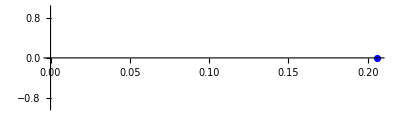

```mathematica
color = {Black,Blue,Green,Pink,Magenta,Red};   tmax = 10; 
dt = 0.001; 
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = 0.20618; y0 =0.0; 
vx0 = 0.0; vy0 = 12.383;
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
α=1.1×10^{-8};
Ms = 1.989×10^{30}; MMs=Ms/Ms
G = 6.67408×10^{-11}; GG=40.27789671; (*GG in AU^3/yr^2 Ms*)
Mm= 2.4 ×10^{23}; Mmm=Mm/Ms;

rNorm     = 0.20618;

Do[
vxList[[nt]] =vxList[[nt-1]] - GG MMs Mmm (1+α/rNorm^2) dt xList[[nt-1]]/rNorm^3;
vyList[[nt]] =vyList[[nt-1]] -GG MMs Mmm (1+α/rNorm^2) dt yList[[nt-1]]/rNorm^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,lt}];
p1 =ListPlot[xylist,PlotStyle->Blue,AspectRatio->0.4]
```